```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
dϕ[x_]:=If[Abs[x]>1,0,If[x>0,-1,If[x==0,0,1]]]
test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
hierarchicalCoefficients[f_,l_]:=Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct[coefficients_]:=Sum[Sum[coefficients[[l,i]] ϕ[2^l(x-2^-l(2i-1))],{i,1,Length[coefficients[[l]]]}],{l,1,Length[coefficients]}]
```

```mathematica
dReconstruct[coefficients_]:=Sum[Sum[coefficients[[l,i]] 2^l dϕ[2^l(x-2^-l(2i-1))],{i,1,Length[coefficients[[l]]]}],{l,1,Length[coefficients]}]
```

```mathematica
test2D[x_,y_]:=Sin[Pi x]^2Sin[Pi y]^2
dytest2D[x_,y_]:=2Pi Sin[Pi x]^2 Sin[Pi y] Cos[Pi y]
```

```mathematica
getCoefficient2D[f_,x_,y_,lx_,ly_]:=f[x,y]-1/2 f[x+2^-lx,y]-1/2 f[x-2^-lx,y]-1/2 f[x,y+2^-ly]-1/2 f[x,y-2^-ly]+1/4 f[x+2^-lx,y+2^-ly]+1/4 f[x-2^-lx,y+2^-ly]+1/4 f[x+2^-lx,y-2^-ly]+1/4 f[x-2^-lx,y-2^-ly]


hierarchicalCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^kx-1,2},{j,1,2^ky-1,2}],{kx,1,lx},{ky,1,ly}]

Reconstruct2D[coefficients_]:=Sum[Sum[coefficients[[lx,ly,i,j]] ϕ[2^lx(x-2^-lx(2i-1))] ϕ[2^ly(y-2^-ly(2j-1))],{i,1,Length[coefficients[[lx,ly]]]},{j,1,Length[coefficients[[lx,ly,i]]]}],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]
```

```mathematica
dxReconstruct2D[coefficients_]:=Sum[Sum[coefficients[[lx,ly,i,j]] 2^lx dϕ[2^lx(x-2^-lx(2i-1))] ϕ[2^ly(y-2^-ly(2j-1))],{i,1,Length[coefficients[[lx,ly]]]},{j,1,Length[coefficients[[lx,ly,i]]]}],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]


dyReconstruct2D[coefficients_]:=Sum[Sum[coefficients[[lx,ly,i,j]] 2^ly  ϕ[2^lx(x-2^-lx(2i-1))] dϕ[2^ly(y-2^-ly(2j-1))],{i,1,Length[coefficients[[lx,ly]]]},{j,1,Length[coefficients[[lx,ly,i]]]}],{lx,1,Length[coefficients]},{ly,1,Length[coefficients[[lx]]]}]
```

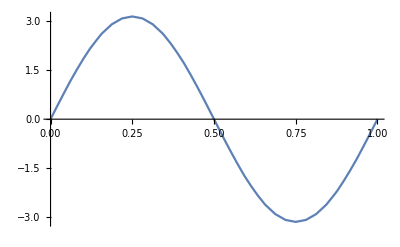

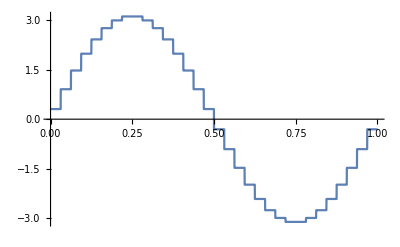

```mathematica
Plot[Reconstruct[N[hierarchicalCoefficients[dtest,5]]],{x,0,1}]
Plot[dReconstruct[N[hierarchicalCoefficients[test,5]]],{x,0,1}]
```

```mathematica
Plot[Reconstruct[hierarchicalCoefficients[dReconstruct[N[hierarchicalCoefficients[test,5]]][#]&],5],{x,0,1}]
```

-Graphics-

```mathematica
Function[x,dReconstruct[N[hierarchicalCoefficients[test,5]]]][t]
```

0.-0.301528 If[32 Abs[-31/32+x]>1,0,If[32 (-31/32+x)>0,-1,If[32 (-31/32+x)==0,0,1]]]-0.562609 If[16 Abs[-15/16+x]>1,0,If[16 (-15/16+x)>0,-1,If[16 (-15/16+x)==0,0,1]]]-0.255623 If[32 Abs[-29/32+x]>1,0,If[32 (-29/32+x)>0,-1,If[32 (-29/32+x)==0,0,1]]]-0.828427 If[8 Abs[-7/8+x]>1,0,If[8 (-7/8+x)>0,-1,If[8 (-7/8+x)==0,0,1]]]-0.170802 If[32 Abs[-27/32+x]>1,0,If[32 (-27/32+x)>0,-1,If[32 (-27/32+x)==0,0,1]]]-0.23304 If[16 Abs[-13/16+x]>1,0,If[16 (-13/16+x)>0,-1,If[16 (-13/16+x)==0,0,1]]]-0.0599777 If[32 Abs[-25/32+x]>1,0,If[32 (-25/32+x)>0,-1,If[32 (-25/32+x)==0,0,1]]]+0.0599777 If[32 Abs[-23/32+x]>1,0,If[32 (-23/32+x)>0,-1,If[32 (-23/32+x)==0,0,1]]]+0.23304 If[16 Abs[-11/16+x]>1,0,If[16 (-11/16+x)>0,-1,If[16 (-11/16+x)==0,0,1]]]+0.170802 If[32 Abs[-21/32+x]>1,0,If[32 (-21/32+x)>0,-1,If[32 (-21/32+x)==0,0,1]]]+0.828427 If[8 Abs[-5/8+x]>1,0,If[8 (-5/8+x)>0,-1,If[8 (-5/8+x)==0,0,1]]]+0.255623 If[32 Abs[-19/32+x]>1,0,If[32 (-19/32+x)>0,-1,If[32 (-19/32+x)==0,0,1]]]+0.562609 If[16 Abs[-9/16+x]>1,0,If[16 (-9/16+x)>0,-1,If[16 (-9/16+x)==0,0,1]]]+0.301528 If[32 Abs[-17/32+x]>1,0,If[32 (-17/32+x)>0,-1,If[32 (-17/32+x)==0,0,1]]]+2. If[2 Abs[-1/2+x]>1,0,If[2 (-1/2+x)>0,-1,If[2 (-1/2+x)==0,0,1]]]+0.301528 If[32 Abs[-15/32+x]>1,0,If[32 (-15/32+x)>0,-1,If[32 (-15/32+x)==0,0,1]]]+0.562609 If[16 Abs[-7/16+x]>1,0,If[16 (-7/16+x)>0,-1,If[16 (-7/16+x)==0,0,1]]]+0.255623 If[32 Abs[-13/32+x]>1,0,If[32 (-13/32+x)>0,-1,If[32 (-13/32+x)==0,0,1]]]+0.828427 If[8 Abs[-3/8+x]>1,0,If[8 (-3/8+x)>0,-1,If[8 (-3/8+x)==0,0,1]]]+0.170802 If[32 Abs[-11/32+x]>1,0,If[32 (-11/32+x)>0,-1,If[32 (-11/32+x)==0,0,1]]]+0.23304 If[16 Abs[-5/16+x]>1,0,If[16 (-5/16+x)>0,-1,If[16 (-5/16+x)==0,0,1]]]+0.0599777 If[32 Abs[-9/32+x]>1,0,If[32 (-9/32+x)>0,-1,If[32 (-9/32+x)==0,0,1]]]-0.0599777 If[32 Abs[-7/32+x]>1,0,If[32 (-7/32+x)>0,-1,If[32 (-7/32+x)==0,0,1]]]-0.23304 If[16 Abs[-3/16+x]>1,0,If[16 (-3/16+x)>0,-1,If[16 (-3/16+x)==0,0,1]]]-0.170802 If[32 Abs[-5/32+x]>1,0,If[32 (-5/32+x)>0,-1,If[32 (-5/32+x)==0,0,1]]]-0.828427 If[8 Abs[-1/8+x]>1,0,If[8 (-1/8+x)>0,-1,If[8 (-1/8+x)==0,0,1]]]-0.255623 If[32 Abs[-3/32+x]>1,0,If[32 (-3/32+x)>0,-1,If[32 (-3/32+x)==0,0,1]]]-0.562609 If[16 Abs[-1/16+x]>1,0,If[16 (-1/16+x)>0,-1,If[16 (-1/16+x)==0,0,1]]]-0.301528 If[32 Abs[-1/32+x]>1,0,If[32 (-1/32+x)>0,-1,If[32 (-1/32+x)==0,0,1]]]

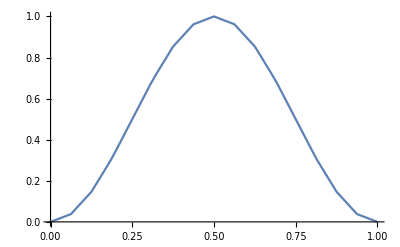

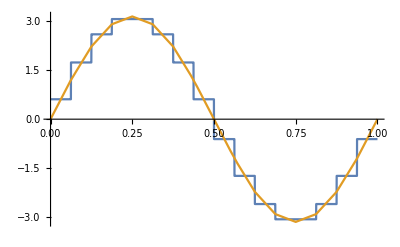

```mathematica
Plot[Reconstruct2D[N[hierarchicalCoefficients2D[test2D,4,4]]]/.x->.5,{y,0,1}]
Plot[{dyReconstruct2D[N[hierarchicalCoefficients2D[test2D,4,4]]]/.x->.5,Reconstruct2D[N[hierarchicalCoefficients2D[dytest2D,4,4]]]/.x->.5},{y,0,1}]
```

```mathematica
Plot3D[{dyReconstruct2D[N[hierarchicalCoefficients2D[test2D,3,3]]],Reconstruct2D[N[hierarchicalCoefficients2D[dytest2D,3,3]]]},{x,0,1},{y,0,1},PlotStyle->{Opacity[.5],Opacity[1]}]
```

-Graphics3D-